```mathematica
spchen = ToExpression[Import["~/Projects/nh_quasiperiodic_disorder/FigS3/chen_spec.csv"]][[2;;-1, ;;]];
```

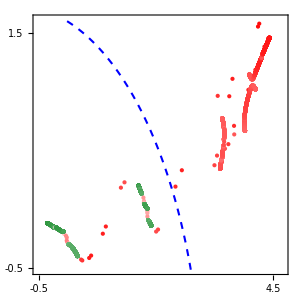

```mathematica
a1 = Show[Graphics[{PointSize[0.01],Table[{ColorData["RedGreenSplit"][x[[3]]],Point[{x[[1]],x[[2]]}]},{x,spchen}]}],ParametricPlot[{4Cos[x] - 1, 2 Sqrt[3] Sin[x] -Sqrt[3] },{x, 0.36, 1.3}, PlotStyle->{Dashed,Blue, Thickness[0.005]}],Frame->True,PlotRange->{{-0.53,4.72}, {-0.51, 1.61}},FrameTicks->{{{-0.5,1.5},None},{{-0.5,4.5},None}},PlotRangePadding->None,LabelStyle->{FontFamily->"Times", FontColor-> Black, 23}, ImagePadding->{{50, 5}, {Automatic, 12}},ImageSize->{300, Automatic}, AspectRatio->1]
```

```mathematica
χchen = ToExpression[Import["~/Projects/nh_quasiperiodic_disorder/FigS3/le_chen.csv"]][[2;;-1, ;;]];
```

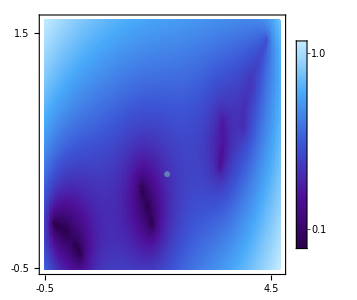

```mathematica
b1 = Show[ListDensityPlot[Take[χchen,{1,Length[χchen],2}], ColorFunction->ColorData["DeepSeaColors"],FrameTicks->{{{-0.5,1.5},None},{{-0.5,4.5},None}},PlotLegends->Placed[BarLegend[Automatic, LegendMarkerSize->{15, 200},Ticks->{0.1,1.0},LabelStyle->{FontFamily->"Times New Roman",16,Black}], Right], PlotRangePadding->None,LabelStyle->{FontFamily->"Times", FontColor-> Black, 23}, ImageSize->{300, Automatic}, AspectRatio->1, ImagePadding->{{50, 5}, {Automatic, 12}}],ListPlot[List /@ {{2.2,.3}},PlotMarkers->{Graphics3D[{RGBColor[1,1,1,0],Sphere[]},Boxed->False],6}]]
```

```mathematica
idosallchen= ToExpression[Import["~/Projects/nh_quasiperiodic_disorder/FigS3/idos_chen.csv"]][[2;;-1, ;;]];idosdetailchen = ToExpression[Import["~/Projects/nh_quasiperiodic_disorder/FigS3/idos_chen_detailed.csv"]][[2;;-1, ;;]];
```

```mathematica
modelchen=NonlinearModelFit[idosdetailchen[[120;;156]], A(1.4574-x)^k+B,{{A, 1.}, {k, -0.5},{B, 0.}},x];
βchen = k/.modelchen["BestFitParameters"]
(βchen + 1)/(βchen+2)
```

-0.434538

0.361211

```mathematica
modelchen[x]
```

-0.0980738+0.163777/(1.4574-x)^0.434538

```mathematica
idosdetailchen[[158]]
```

{1.457,4.81402}

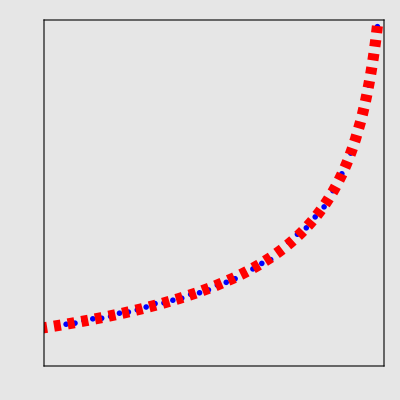

```mathematica
fitc1 = Show[ListPlot[idosdetailchen[[120;;156]](*idosdetail25[[300;;631]]*), PlotTheme->"Scientific", PlotRange->{All, {0.4,All}},FrameTicks->None, ImageSize->{80}, AspectRatio->1, PlotMarkers->{"OpenMarkers",2}, PlotStyle->Blue],(*ListPlot[idosdetail25[[500;;629]], PlotStyle->{Blue,PointSize[.02]}], *)Plot[modelchen[x], {x, 1.4, 1.5},PlotStyle->{Red,Dashed, Thickness[0.02]}, PlotRange->All],Background->GrayLevel[0.9,0.9]]
```

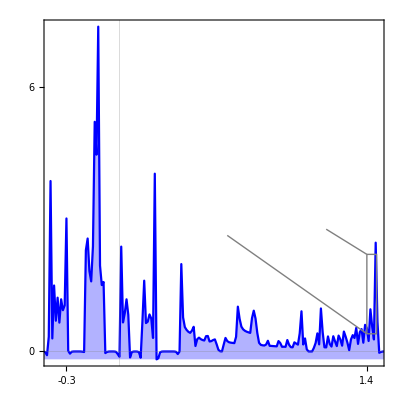

```mathematica
c1 = Show[ListLinePlot[idosallchen, PlotTheme->"Scientific", PlotStyle->{Blue},Filling->Bottom,PlotRange->{{-0.39, 1.46}, All}, AspectRatio->1, ImageSize->{275}, FrameTicks->{{{0,6},None},{{-0.3,1.4},None}},LabelStyle->{FontFamily->"Times", FontColor-> Black, 23},Epilog->{Inset[fitc1, {0.9, 4}]}],
Graphics[{GrayLevel[0.5],Line[{{1.4, 0.4}, {1.4, 2.2},{1.455, 2.2},{1.455,0.4},{1.4, 0.4}}]}],Graphics[{GrayLevel[0.5],Line[{{1.4, 0.4}, {0.61, 2.63}}]}],Graphics[{GrayLevel[0.5],Line[{{1.4, 2.2}, {1.17, 2.77}}]}]]
```

```mathematica
chenevo =ToExpression[Import["~/Projects/nh_quasiperiodic_disorder/FigS3/chen_evo.csv"]][[2;;-1, ;;]];
```

```mathematica
lm = LinearModelFit[chenevo[[50;;-1]],x,x]
d1 = Show[ListPlot[chenevo, PlotMarkers->{Automatic, Small},PlotTheme->"Frame", Epilog->{Inset[Style["δ="<>ToString[NumberForm[lm["BestFitParameters"][[2]],{2,2}]],FontFamily->"Times", FontSize->23],{Log[10],Log[7]}]},PlotStyle->RGBColor[0, .5, 1],FrameTicks->{{{{Log[0.1],"0.1"},{Log[1],"1"},{Log[10],"10"}},None},{{{Log[0.1], "0.1"},{Log[1],"1"},{Log[10],"10"},{Log[100],"100"},{Log[1000],"1000"}},None}},PlotRange->All,LabelStyle->{FontFamily->"Times", FontColor-> Black, 23},ImageSize->{290}],Plot[lm[x],{x,1,11}, PlotStyle->{GrayLevel[0.7], Dashed, Thickness[0.01]}], AspectRatio->1]
```

FittedModel[…]

-Graphics-

```mathematica
sprand = ToExpression[Import["~/Projects/nh_quasiperiodic_disorder/FigS3/rand_spec.csv"]][[2;;-1, ;;]];
```

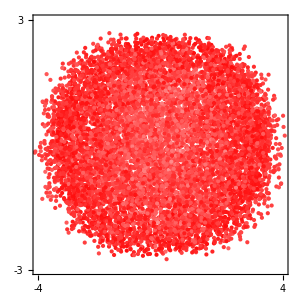

```mathematica
a2 = Show[Graphics[{PointSize[0.01],Table[{ColorData["RedGreenSplit"][x[[3]]],Point[{x[[1]],x[[2]]}]},{x,sprand}]}],Frame->True,FrameTicks->{{{-3,3},None},{{-4,4},None}},PlotRangePadding->None,PlotRange->{{-4,4}, {-3, 3}},LabelStyle->{FontFamily->"Times", FontColor-> Black, 23}, ImagePadding->{{50, 5}, {Automatic, 12}},ImageSize->{300, Automatic}, AspectRatio->1]
```

```mathematica
χrand = ToExpression[Import["~/Projects/nh_quasiperiodic_disorder/FigS3/le_rand.csv"]][[2;;-1, ;;]];
```

```mathematica
b2 = Show[ListDensityPlot[Take[χrand,{1,Length[χrand],3}], ColorFunction->ColorData["DeepSeaColors"],PlotRange->{{-4,4},{-3,3}},FrameTicks->{{{-3,3},None},{{-4,4},None}},PlotLegends->Placed[BarLegend[Automatic, LegendMarkerSize->{15, 200},Ticks->{0.1,1.6},LabelStyle->{FontFamily->"Times New Roman",16,Black}], Right], PlotRangePadding->None,LabelStyle->{FontFamily->"Times", FontColor-> Black, 23}, ImagePadding->{{50, 5}, {Automatic, 12}},ImageSize->{300, Automatic}, AspectRatio->1],ListPlot[List /@ {{2.2,.3}},PlotMarkers->{Graphics3D[{RGBColor[1,1,1,0],Sphere[]},Boxed->False],6}]]
```

-Graphics-

```mathematica
idosallrand= ToExpression[Import["~/Projects/nh_quasiperiodic_disorder/FigS3/idos_rand.csv"]][[2;;-1, ;;]];idosdetailrand = ToExpression[Import["~/Projects/nh_quasiperiodic_disorder/FigS3/idos_rand_detailed.csv"]][[2;;-1, ;;]];
```

```mathematica
modelchen=NonlinearModelFit[idosdetailchen[[120;;156]], A(1.4574-x)^k+B,{{A, 1.}, {k, -0.5},{B, 0.}},x];
βchen = k/.modelchen["BestFitParameters"]
(βchen + 1)/(βchen+2)
```

-0.434538

0.361211

```mathematica
modelchen[x]
```

-0.0980738+0.163777/(1.4574-x)^0.434538

```mathematica
Dimensions@idosdetailrand
```

{1001,2}

```mathematica
fitc2 = Show[ListPlot[idosdetailrand[[;;]](*idosdetail25[[300;;631]]*), PlotTheme->"Scientific", PlotRange->{All, All},(*FrameTicks->None,*) ImageSize->{80}, AspectRatio->1, PlotMarkers->{"OpenMarkers",2}, PlotStyle->Blue],(*ListPlot[idosdetail25[[500;;629]], PlotStyle->{Blue,PointSize[.02]}], *)(*Plot[modelchen[x], {x, 1.4, 1.5},PlotStyle->{Red,Dashed, Thickness[0.02]}, PlotRange->All],*)Background->GrayLevel[0.9,0.9]]
```

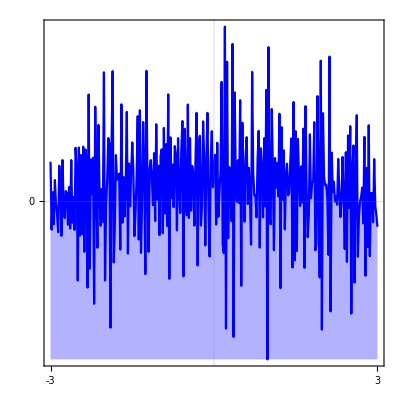

```mathematica
c2 = Show[ListLinePlot[idosallrand, PlotTheme->"Scientific", PlotStyle->{Blue},Filling->Bottom,PlotRange->{{-3, 3}, All}, AspectRatio->1, ImageSize->{275}, FrameTicks->{{{0,2},None},{{-3,3},None}},LabelStyle->{FontFamily->"Times", FontColor-> Black, 23}(*,Epilog->{Inset[fitb, {0.25, 6}]}*)](*,
Graphics[{GrayLevel[0.5],Line[{{0.419, 0.3025}, {0.419, 1.5},{0.524, 1.5},{0.524,0.3025},{0.419, 0.3025}}]}],Graphics[{GrayLevel[0.5],Line[{{0.523, 1.5}, {0.406, 4.6}}]}],Graphics[{GrayLevel[0.5],Line[{{0.419, 1.5}, {0.093, 4.6}}]}]*)]
```

```mathematica
randevo =ToExpression[Import["~/Projects/nh_quasiperiodic_disorder/FigS3/rand_evo.csv"]][[2;;-1, ;;]];
```

```mathematica
lm = LinearModelFit[randevo[[50;;-1]],x,x]
d2 = Show[ListPlot[randevo, PlotMarkers->{Automatic, Small},PlotTheme->"Frame", Epilog->{Inset[Style["δ="<>ToString[NumberForm[lm["BestFitParameters"][[2]],{2,2}]],FontFamily->"Times", FontSize->23],{Log[10],Log[40]}]},PlotStyle->RGBColor[0, .5, 1],FrameTicks->{{{{Log[1],"1"},{Log[81],"81"}},None},{{{Log[1],"1"},{Log[10],"10"},{Log[100],"100"},{Log[1000],"1000"}},None}},PlotRange->All,LabelStyle->{FontFamily->"Times", FontColor-> Black, 23},ImageSize->{290}],Plot[lm[x],{x,1,11}, PlotStyle->{GrayLevel[0.7], Dashed, Thickness[0.01]}], AspectRatio->1]
```

FittedModel[…]

-Graphics-

```mathematica
BarLegend[{"RedGreenSplit",{0,1}},LegendMarkerSize->{15, 200},Ticks->{0,1},LabelStyle->{FontFamily->"Times New Roman",16,Black}]
```

```mathematica
FigS3 = ListPlot[{{0,0}},PlotStyle->Opacity[0],PlotRange->{{0,1},{0,1}},ImageSize->{1260,Automatic},Axes->None,Epilog->{Inset[a1,{.1245,0.765}], Inset[a2,{.1245,0.245}],Inset[b1,{.41,0.765}], Inset[b2,{.41,0.245}],Inset[c1,{.66,0.755}], Inset[c2,{.66,0.235}],Inset[d1,{.885,0.755}], Inset[d2,{.885,0.235}],
Inset[BarLegend[{"RedGreenSplit",{0,1}},LegendMarkerSize->{15, 200},Ticks->{0,1},LabelStyle->{FontFamily->"Times New Roman",16,Black}], {0.26, 0.775}],Inset[BarLegend[{"RedGreenSplit",{0,1}},LegendMarkerSize->{15, 200},Ticks->{0,1},LabelStyle->{FontFamily->"Times New Roman",16,Black}], {0.26, 0.255}],
Inset[Rotate[Row[{Style["ρ(Im",23,FontFamily->"Times"],Style["E)",23,FontFamily->"Times",Italic]}],Pi/2],{0.555,0.78}],Inset[Rotate[Row[{Style["Im",23,FontFamily->"Times"],Style["E",23,FontFamily->"Times",Italic]}],Pi/2],{0.03,0.78}],Inset[Rotate[Row[{Style["",23,FontFamily->"Times"],Style["X(t)",23,FontFamily->"Times",Italic]}],Pi/2],{0.78,0.78}],Inset[Rotate[Row[{Style["Im",23,FontFamily->"Times"],Style["E",23,FontFamily->"Times",Italic]}],Pi/2],{0.295,0.78}],Inset[Rotate[Row[{Style["ρ(Im",23,FontFamily->"Times"],Style["E)",23,FontFamily->"Times",Italic]}],Pi/2],{0.55,0.27}],Inset[Rotate[Row[{Style["Im",23,FontFamily->"Times"],Style["E",23,FontFamily->"Times",Italic]}],Pi/2],{0.03,0.27}],Inset[Rotate[Row[{Style["",23,FontFamily->"Times"],Style["X(t)",23,FontFamily->"Times",Italic]}],Pi/2],{0.78,0.27}],Inset[Rotate[Row[{Style["Im",23,FontFamily->"Times"],Style["E",23,FontFamily->"Times",Italic]}],Pi/2],{0.295,0.27}],Inset[Row[{Style["Re",23,FontFamily->"Times"],Style["E",23,FontFamily->"Times",Italic]}], {0.137, 0.02}],Inset[Row[{Style["Re",23,FontFamily->"Times"],Style["E",23,FontFamily->"Times",Italic]}], {0.4, 0.02}],Inset[Row[{Style["Im",23,FontFamily->"Times"],Style["E",23,FontFamily->"Times",Italic]}], {0.665, 0.02}],Inset[Row[{Style["",23,FontFamily->"Times"],Style["t",23,FontFamily->"Times",Italic]}], {0.887, 0.02}],Inset[Row[{Style["Re",23,FontFamily->"Times"],Style["E",23,FontFamily->"Times",Italic]}], {0.137, 0.53}],Inset[Row[{Style["Re",23,FontFamily->"Times"],Style["E",23,FontFamily->"Times",Italic]}], {0.4, 0.53}],Inset[Row[{Style["Im",23,FontFamily->"Times"],Style["E",23,FontFamily->"Times",Italic]}], {0.665, 0.53}],Inset[Row[{Style["",23,FontFamily->"Times"],Style["t",23,FontFamily->"Times",Italic]}], {0.887, 0.53}],
Inset[Style["(a1)",26,FontFamily->Times],{.065,0.95}],Inset[Style["(a2)",23,FontFamily->Times],{.065,0.43}],
Inset[Style["(b1)",26,FontFamily->Times],{.325,0.95}],Inset[Style["(b2)",23,FontFamily->Times],{.325,0.43}],
Inset[Style["(c1)",26,FontFamily->Times],{.585,0.95}],Inset[Style["(c2)",23,FontFamily->Times],{.585,0.43}],
Inset[Style["(d1)",26,FontFamily->Times],{.81,0.95}],Inset[Style["(d2)",23,FontFamily->Times],{.81,0.43}],Inset[Style["FD",18,FontFamily->Times], {0.258, 0.94}],Inset[Style["FD",18,FontFamily->Times], {0.258, 0.42}],Inset[Row[{Style["γ(",23,FontFamily->"Times"],Style["E)",18,FontFamily->"Times",Italic]}], {0.522, 0.42}],Inset[Row[{Style["γ(",23,FontFamily->"Times"],Style["E)",18,FontFamily->"Times",Italic]}], {0.522, 0.94}]}, AspectRatio->0.48]
```

-Graphics-

```mathematica
Export["/Users/xingzy/Projects/nh_quasiperiodic_disorder/FigS3/FigS3.pdf",FigS3,"PDF"]
```

/Users/xingzy/Projects/nh_quasiperiodic_disorder/FigS3/FigS3.pdf

```mathematica
FigS3 = ListPlot[{{0,0}},PlotStyle->Opacity[0],PlotRange->{{0,1},{0,1}},ImageSize->{1260,Automatic},Axes->None,Epilog->{Inset[a1,{.1245,0.505}],Inset[b1,{.41,0.505}],Inset[c1,{.66,0.495}],Inset[d1,{.885,0.495}],
Inset[BarLegend[{"RedGreenSplit",{0,1}},LegendMarkerSize->{15, 200},Ticks->{0,1},LabelStyle->{FontFamily->"Times New Roman",16,Black}], {0.26, 0.525}],
Inset[Rotate[Row[{Style["ρ(Im",23,FontFamily->"Times"],Style["E)",23,FontFamily->"Times",Italic]}],Pi/2],{0.555,0.53}],Inset[Rotate[Row[{Style["Im",23,FontFamily->"Times"],Style["E",23,FontFamily->"Times",Italic]}],Pi/2],{0.03,0.53}],Inset[Rotate[Row[{Style["",23,FontFamily->"Times"],Style["X(t)",23,FontFamily->"Times",Italic]}],Pi/2],{0.78,0.53}],Inset[Rotate[Row[{Style["Im",23,FontFamily->"Times"],Style["E",23,FontFamily->"Times",Italic]}],Pi/2],{0.295,0.53}],Inset[Row[{Style["Re",23,FontFamily->"Times"],Style["E",23,FontFamily->"Times",Italic]}], {0.137, 0.05}],Inset[Row[{Style["Re",23,FontFamily->"Times"],Style["E",23,FontFamily->"Times",Italic]}], {0.4, 0.05}],Inset[Row[{Style["Im",23,FontFamily->"Times"],Style["E",23,FontFamily->"Times",Italic]}], {0.665, 0.05}],Inset[Row[{Style["",23,FontFamily->"Times"],Style["t",23,FontFamily->"Times",Italic]}], {0.887, 0.05}],
Inset[Style["(a)",26,FontFamily->Times],{.065,0.89}],
Inset[Style["(b)",26,FontFamily->Times],{.325,0.89}],
Inset[Style["(c)",26,FontFamily->Times],{.585,0.89}],
Inset[Style["(d)",26,FontFamily->Times],{.81,0.89}],Inset[Style["FD",18,FontFamily->Times], {0.258, 0.87}],Inset[Row[{Style["γ(",23,FontFamily->"Times"],Style["E)",18,FontFamily->"Times",Italic]}], {0.522, 0.87}]}, AspectRatio->0.24]
```

-Graphics-

```mathematica
Export["/Users/xingzy/Projects/nh_quasiperiodic_disorder/FigS3/FigS.pdf",FigS3,"PDF"]
```

/Users/xingzy/Projects/nh_quasiperiodic_disorder/FigS3/FigS.pdf